```mathematica
Clear["Global`"]
```

```mathematica
V22={0.9,0.93,0.87,2.13,9.57,21.9,42,59.77,78.57,94.43,113.6}
```

{0.9,0.93,0.87,2.13,9.57,21.9,42,59.77,78.57,94.43,113.6}

```mathematica
V24={2.77,8.57,24.4,50.27,77.8,102.63,118.4,139.77,148,162.5,168.4,177.87,194.47}
```

{2.77,8.57,24.4,50.27,77.8,102.63,118.4,139.77,148,162.5,168.4,177.87,194.47}

```mathematica
V26={2.3,3.6,10.4,29.35,63.8,102.8,132.9,159.15,184.65,191.9,211.05,218.15,228.3,234.15,236.95,240.35,248.2,272.15}
```

{2.3,3.6,10.4,29.35,63.8,102.8,132.9,159.15,184.65,191.9,211.05,218.15,228.3,234.15,236.95,240.35,248.2,272.15}

```mathematica
V28= {1.6,2.1,2.25,3.1,4.7,6.6,23,58,107.5,158.7,197.75,221.55,240.65,262.15,273.05,281.3,295.25,295.55,299.3,304.9,302.65,299.75,303.85}
```

{1.6,2.1,2.25,3.1,4.7,6.6,23,58,107.5,158.7,197.75,221.55,240.65,262.15,273.05,281.3,295.25,295.55,299.3,304.9,302.65,299.75,303.85}

```mathematica
V30={2.6,3.4,3.3,3.6,2.9,4,3.6,5.3,11,32.3,81.8,137.2,210,264.4,300.9,329.3,338.7,357.1,356.8,369,375,380,377.2,383.1,370.3,375.2,368.5,354.6,358.5}
```

{2.6,3.4,3.3,3.6,2.9,4,3.6,5.3,11,32.3,81.8,137.2,210,264.4,300.9,329.3,338.7,357.1,356.8,369,375,380,377.2,383.1,370.3,375.2,368.5,354.6,358.5}

```mathematica
V32={5,3.4,4.1,4,5.1,3.7,4.7,3.3,3.9,4.7,4.106666667,4.091515152,4.076363636,4.061212121,4.046060606,4.030909091,4.015757576,4.000606061,3.985454545,3.97030303,3.955151515,3.94,3.924848485,3.90969697,3.894545455,3.879393939,3.864242424,3.849090909,3.833939394,3.818787879,3.803636364,3.788484848,3.773333333,3.758181818,3.743030303,3.727878788}
```

{5,3.4,4.1,4,5.1,3.7,4.7,3.3,3.9,4.7,4.10667,4.09152,4.07636,4.06121,4.04606,4.03091,4.01576,4.00061,3.98545,3.9703,3.95515,3.94,3.92485,3.9097,3.89455,3.87939,3.86424,3.84909,3.83394,3.81879,3.80364,3.78848,3.77333,3.75818,3.74303,3.72788}

```mathematica
V34={5.7,4.1,5.4,5,5.5,7.9,5,7.7,8.3,8.4,18,52.1,123.2,234.7,354.1,446,501.8,545.8,560.8,563.7,574,582,573.6,567.2,560.3,553.5,539.6,542.6,524.9,510.8,513.9,505,487.2,483.6,466.5,470.5}
```

{5.7,4.1,5.4,5,5.5,7.9,5,7.7,8.3,8.4,18,52.1,123.2,234.7,354.1,446,501.8,545.8,560.8,563.7,574,582,573.6,567.2,560.3,553.5,539.6,542.6,524.9,510.8,513.9,505,487.2,483.6,466.5,470.5}

```mathematica
V35={6.1,4.5,7,6.4,6.6,6.3,6.3,7,9.9,24.5,59.9,153.8,268.7,403.3,496.7,567.9,587.6,637.4,635,641.3,647.8,640.3,630.1,619.9,607.7,596.1,575.9,567.5,558.3,540.7,544.9,532.6,508.6,502.7,496.9,495.3}
```

{6.1,4.5,7,6.4,6.6,6.3,6.3,7,9.9,24.5,59.9,153.8,268.7,403.3,496.7,567.9,587.6,637.4,635,641.3,647.8,640.3,630.1,619.9,607.7,596.1,575.9,567.5,558.3,540.7,544.9,532.6,508.6,502.7,496.9,495.3}

```mathematica
λ={24.6,25.6,26.6,27.6,28.5,29.5,30.5,31.5,32.5,33.4,34.4,35.4,36.4,37.4,38.4,39.3,40.3,41.3,42.3,43.3,44.3,45.2,46.2,47.2,48.2,49.2,50.1,51.1,52.1,53.1,54.1,55,56,57,58,59,59.9,60.9}
```

{24.6,25.6,26.6,27.6,28.5,29.5,30.5,31.5,32.5,33.4,34.4,35.4,36.4,37.4,38.4,39.3,40.3,41.3,42.3,43.3,44.3,45.2,46.2,47.2,48.2,49.2,50.1,51.1,52.1,53.1,54.1,55,56,57,58,59,59.9,60.9}

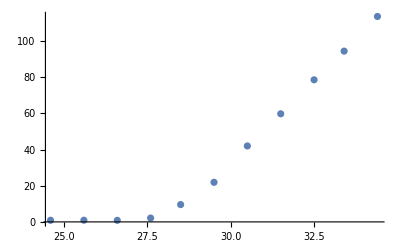

```mathematica
l1=ListPlot[Table[{λ[[i]],V22[[i]]},{i,Length[V22]}]]
l2=ListPlot[Table[{λ[[Length[V24]-i]],V24[[Length[V24]-i]]},{i,Length[V24]}],PlotStyle->Gray];
l3=ListPlot[Table[{λ[[i]],V26[[i]]},{i,Length[V26]}]];

l4=ListPlot[Table[{λ[[Length[V28]-i]],V28[[Length[V28]-i]]},{i,Length[V28]}],PlotStyle->Blue];
l5=ListPlot[Table[{λ[[i+2]],V30[[i]]},{i,Length[V30]}]];
l6=ListPlot[Table[{λ[[Length[V32]-i]],V32[[Length[V32]-i]]},{i,Length[V32]}],PlotStyle->Black];
l7=ListPlot[Table[{λ[[i+2]],V34[[i]]},{i,Length[V34]}]];
l8=ListPlot[Table[{λ[[Length[V35]-i]],V35[[Length[V35]-i]]},{i,Length[V35]}],PlotStyle->Red];
```

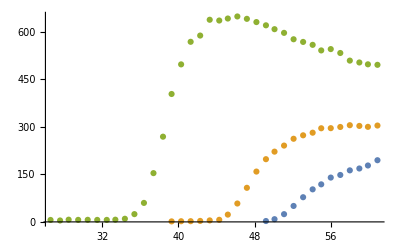

```mathematica
ListPlot[{Table[{λ[[Length[λ]-Length[V24]+ i]],V24[[i]]},{i,Length[V24]}],Table[{λ[[Length[λ]-Length[V28]+ i]],V28[[i]]},{i,Length[V28]}],Table[{λ[[Length[λ]-Length[V35]+ i]],V35[[i]]},{i,Length[V35]}]}]
```

```mathematica
Show[%374,AxesLabel->{HoldForm["x"],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%374,AxesLabel→{x,None},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
Show[%374,AxesLabel->{HoldForm["y"],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%374,AxesLabel→{y,None},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

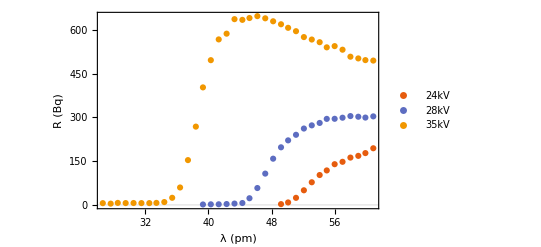

```mathematica
ListPlot[{Table[{λ[[Length[λ]-Length[V24]+ i]],V24[[i]]},{i,Length[V24]}],Table[{λ[[Length[λ]-Length[V28]+ i]],V28[[i]]},{i,Length[V28]}],Table[{λ[[Length[λ]-Length[V35]+ i]],V35[[i]]},{i,Length[V35]}]},PlotTheme->"Scientific",PlotLegends->{"24kV","28kV","35kV"},FrameLabel->{HoldForm["λ (pm)"],HoldForm["R (Bq)"]}]
```

```mathematica
Rasterize[%368]
```

-Graphics-

```mathematica
Show[%368,AxesLabel->{HoldForm["λ (pm)"],HoldForm["R (Bq)"]}]
```

Show::gtype: Out is not a type of graphics.

Show[%378,AxesLabel→{λ (pm),R (Bq)}]

```mathematica
Show[%368,AxesLabel->{HoldForm["λ (pm)"],HoldForm["R (Bq)"]},PlotLegends->{"U1","U2","U3"}]
```

Show::gtype: Out is not a type of graphics.

Show[%374,AxesLabel→{λ (pm),R (Bq)},PlotLegends→{U1,U2,U3}]

```mathematica
ListPlot[l
```

```mathematica
Show[%374,AxesLabel->{HoldForm["λ (pm)"],HoldForm["R (Bq)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%374,AxesLabel→{λ (pm),R (Bq)},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

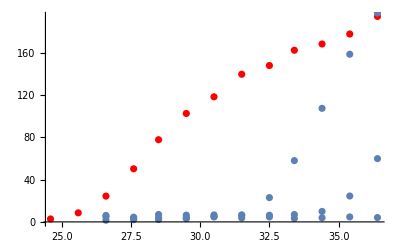

-Graphics-

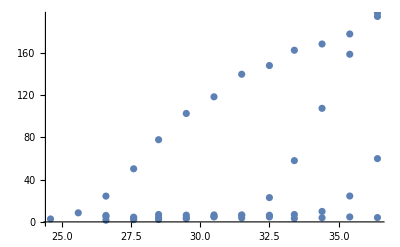

-Graphics-

```mathematica
ListPlot[{Table[{λ[[Length[λ]-Length[V24]+ i]],V24[[i]]},{i,Length[V24]}],Table[{λ[[Length[λ]-Length[V28]+ i]],V28[[i]]},{i,Length[V28]}],Table[{λ[[Length[λ]-Length[V35]+ i]],V35[[i]]},{i,Length[V35]}]}]
```

-Graphics-